```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
d1=Import["trials_with_entities/trial1.out","List"];
d2=Import["trials_no_entities/trial1.out","List"];
```

Total memory differences (in MB) :
NB: I don’t show the average for all 3 trials here but all three trials were very close.

```mathematica
d1[[-1]]-d1[[1]]
d2[[-1]]-d2[[1]]
```

278.641

60.9922

### Use 4 different models to determine memory growth: - Basic linear model - 3 parameter exponential model - 3 parameter power function - third degree polynomial

### Fits for memory usage on parsing data with no preprocessing

```mathematica
f1=LinearModelFit[d1,x,x]
f2=NonlinearModelFit[d1,a+b*c^x,{a,b,c},x]
f3=NonlinearModelFit[d1,a+b*x^c,{a,b,c},x]
f4=NonlinearModelFit[d1,a*x+b*x^2+c*x^3,{a,b,c},x]
```

FittedModel[766.075+2.10339 x]

FittedModel[770.082+28.2249 1.02171^x]

FittedModel[806.986+0.00663811 x^2.24302]

FittedModel[57.5426 x-1.08319 x^2+0.00617395 x^3]

```mathematica
h[fit_]:=fit["AdjustedRSquared"]
Map[h,{f1,f2,f3,f4}]
```

{0.81751,0.999321,0.999361,0.947572}

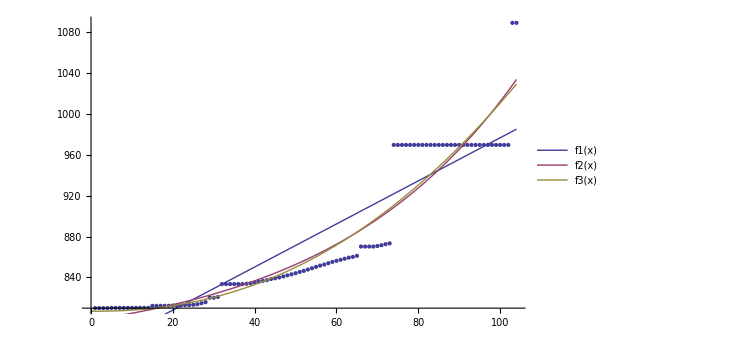

```mathematica
Show[ListPlot[d1], Plot[{f1[x], f2[x],f3[x]},{x, 0,Length[d1]}, PlotLegends->"Expressions"]]
```

### Fits for memory usage on parsing data with preprocessing to remove URLs, hashtags, and twitter mentions

```mathematica
g1=LinearModelFit[d1,x,x]
g2=NonlinearModelFit[d2,a+b*c^x,{a,b,c},x]
g3=NonlinearModelFit[d2,a+b*x^c,{a,b,c},x]
g4=NonlinearModelFit[d2,a*x+b*x^2+c*x^3,{a,b,c},x]
```

FittedModel[766.075+2.10339 x]

FittedModel[789.612+13.3802 1.01871^x]

FittedModel[805.76+0.00693981 x^1.99609]

FittedModel[58.9255 x-1.14261 x^2+0.00654039 x^3]

```mathematica
h[fit_]:=fit["AdjustedRSquared"]
Map[h,{g1,g2,g3,g4}]
```

{0.81751,0.999962,0.999963,0.94354}

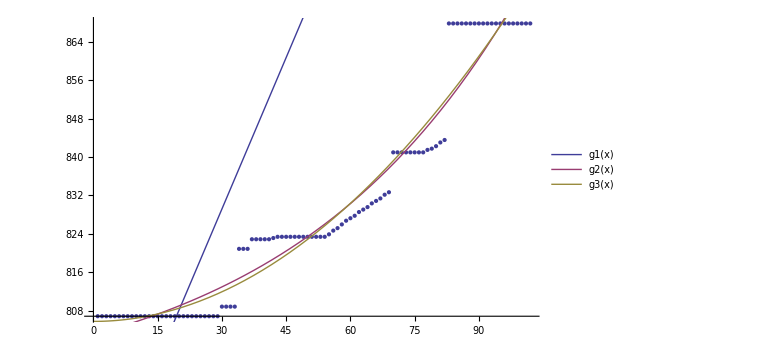

```mathematica
Show[ListPlot[d2], Plot[{g1[x], g2[x],g3[x]},{x, 0,Length[d2]}, PlotLegends->"Expressions"]]
```

```mathematica
(1009737 - 995565)/1009737.0
```

0.0140353